```mathematica
trun1=(Subscript[ϕ, 0][x]+Subscript[ϕ, 1/3][x]χ[y/3]+Subscript[ϕ, -1/3][x]χ[-y/3]+Subscript[ϕ, 2/3][x]χ[2y/3]+Subscript[ϕ, -2/3][x]χ[-2y/3])D[D[(Subscript[ϕ, 0][x]+3^s Subscript[ϕ, 1/3][x]χ[y/3]+3^s Subscript[ϕ, -1/3][x]χ[-y/3]+3^s Subscript[ϕ, 2/3][x]χ[2y/3]+3^s Subscript[ϕ, -2/3][x]χ[-2y/3]), x], x]/.{χ->(ⅇ^(2π ⅈ #)&)};
```

```mathematica
trun1//Expand
```

3^s ⅇ^(-8/3 ⅈ π y) ϕ_(-2/3)[x] ϕ_(-2/3)''[x]+3^s ⅇ^(-2 ⅈ π y) ϕ_(-1/3)[x] ϕ_(-2/3)''[x]+3^s ⅇ^(-4/3 ⅈ π y) ϕ_0[x] ϕ_(-2/3)''[x]+3^s ⅇ^(-2/3 ⅈ π y) ϕ_(1/3)[x] ϕ_(-2/3)''[x]+3^s ϕ_(2/3)[x] ϕ_(-2/3)''[x]+3^s ⅇ^(-2 ⅈ π y) ϕ_(-2/3)[x] ϕ_(-1/3)''[x]+3^s ⅇ^(-4/3 ⅈ π y) ϕ_(-1/3)[x] ϕ_(-1/3)''[x]+3^s ⅇ^(-2/3 ⅈ π y) ϕ_0[x] ϕ_(-1/3)''[x]+3^s ϕ_(1/3)[x] ϕ_(-1/3)''[x]+3^s ⅇ^((2 ⅈ π y)/3) ϕ_(2/3)[x] ϕ_(-1/3)''[x]+ⅇ^(-4/3 ⅈ π y) ϕ_(-2/3)[x] ϕ_0''[x]+ⅇ^(-2/3 ⅈ π y) ϕ_(-1/3)[x] ϕ_0''[x]+ϕ_0[x] ϕ_0''[x]+ⅇ^((2 ⅈ π y)/3) ϕ_(1/3)[x] ϕ_0''[x]+ⅇ^((4 ⅈ π y)/3) ϕ_(2/3)[x] ϕ_0''[x]+3^s ⅇ^(-2/3 ⅈ π y) ϕ_(-2/3)[x] ϕ_(1/3)''[x]+3^s ϕ_(-1/3)[x] ϕ_(1/3)''[x]+3^s ⅇ^((2 ⅈ π y)/3) ϕ_0[x] ϕ_(1/3)''[x]+3^s ⅇ^((4 ⅈ π y)/3) ϕ_(1/3)[x] ϕ_(1/3)''[x]+3^s ⅇ^(2 ⅈ π y) ϕ_(2/3)[x] ϕ_(1/3)''[x]+3^s ϕ_(-2/3)[x] ϕ_(2/3)''[x]+3^s ⅇ^((2 ⅈ π y)/3) ϕ_(-1/3)[x] ϕ_(2/3)''[x]+3^s ⅇ^((4 ⅈ π y)/3) ϕ_0[x] ϕ_(2/3)''[x]+3^s ⅇ^(2 ⅈ π y) ϕ_(1/3)[x] ϕ_(2/3)''[x]+3^s ⅇ^((8 ⅈ π y)/3) ϕ_(2/3)[x] ϕ_(2/3)''[x]

```mathematica
Sum[trun1,{y,0,2}]/3//FullSimplify
```

ϕ_0[x] ϕ_0''[x]+3^s (ϕ_(-1/3)[x]+ϕ_(2/3)[x]) (ϕ_(-2/3)''[x]+ϕ_(1/3)''[x])+3^s (ϕ_(-2/3)[x]+ϕ_(1/3)[x]) (ϕ_(-1/3)''[x]+ϕ_(2/3)''[x])

```mathematica
1/p(-1+1/(1-p^-1)(p-1)/p)//FullSimplify
```

0

```mathematica
trun11=(Subscript[ϕ, 0][x]+Subscript[ϕ, 1/3][x]χ[y/3]+Subscript[ϕ, -1/3][x]χ[-y/3]+Subscript[ϕ, 2/3][x]χ[2y/3]+Subscript[ϕ, -2/3][x]χ[-2y/3])^2/.{χ->(ⅇ^(2π ⅈ #)&)};
```

```mathematica
trun11//Expand
```

ⅇ^(-8/3 ⅈ π y) (ϕ_(-2/3)[x])^2+2 ⅇ^(-2 ⅈ π y) ϕ_(-2/3)[x] ϕ_(-1/3)[x]+ⅇ^(-4/3 ⅈ π y) (ϕ_(-1/3)[x])^2+2 ⅇ^(-4/3 ⅈ π y) ϕ_(-2/3)[x] ϕ_0[x]+2 ⅇ^(-2/3 ⅈ π y) ϕ_(-1/3)[x] ϕ_0[x]+ϕ_0[x]^2+2 ⅇ^(-2/3 ⅈ π y) ϕ_(-2/3)[x] ϕ_(1/3)[x]+2 ϕ_(-1/3)[x] ϕ_(1/3)[x]+2 ⅇ^((2 ⅈ π y)/3) ϕ_0[x] ϕ_(1/3)[x]+ⅇ^((4 ⅈ π y)/3) (ϕ_(1/3)[x])^2+2 ϕ_(-2/3)[x] ϕ_(2/3)[x]+2 ⅇ^((2 ⅈ π y)/3) ϕ_(-1/3)[x] ϕ_(2/3)[x]+2 ⅇ^((4 ⅈ π y)/3) ϕ_0[x] ϕ_(2/3)[x]+2 ⅇ^(2 ⅈ π y) ϕ_(1/3)[x] ϕ_(2/3)[x]+ⅇ^((8 ⅈ π y)/3) (ϕ_(2/3)[x])^2

```mathematica
Sum[trun11,{y,0,2}]/3//FullSimplify
```

ϕ_0[x]^2+2 (ϕ_(-2/3)[x]+ϕ_(1/3)[x]) (ϕ_(-1/3)[x]+ϕ_(2/3)[x])

```mathematica
trun111=(Subscript[ϕ, 0][x]+Subscript[ϕ, 1/3][x]χ[y/3]+Subscript[ϕ, -1/3][x]χ[-y/3]+Subscript[ϕ, 2/3][x]χ[2y/3]+Subscript[ϕ, -2/3][x]χ[-2y/3])^3/.{χ->(ⅇ^(2π ⅈ #)&)};
```

```mathematica
trun111=trun111//Expand
```

ⅇ^(-4 ⅈ π y) (ϕ_(-2/3)[x])^3+3 ⅇ^(-10/3 ⅈ π y) (ϕ_(-2/3)[x])^2 ϕ_(-1/3)[x]+3 ⅇ^(-8/3 ⅈ π y) ϕ_(-2/3)[x] (ϕ_(-1/3)[x])^2+ⅇ^(-2 ⅈ π y) (ϕ_(-1/3)[x])^3+3 ⅇ^(-8/3 ⅈ π y) (ϕ_(-2/3)[x])^2 ϕ_0[x]+6 ⅇ^(-2 ⅈ π y) ϕ_(-2/3)[x] ϕ_(-1/3)[x] ϕ_0[x]+3 ⅇ^(-4/3 ⅈ π y) (ϕ_(-1/3)[x])^2 ϕ_0[x]+3 ⅇ^(-4/3 ⅈ π y) ϕ_(-2/3)[x] ϕ_0[x]^2+3 ⅇ^(-2/3 ⅈ π y) ϕ_(-1/3)[x] ϕ_0[x]^2+ϕ_0[x]^3+3 ⅇ^(-2 ⅈ π y) (ϕ_(-2/3)[x])^2 ϕ_(1/3)[x]+6 ⅇ^(-4/3 ⅈ π y) ϕ_(-2/3)[x] ϕ_(-1/3)[x] ϕ_(1/3)[x]+3 ⅇ^(-2/3 ⅈ π y) (ϕ_(-1/3)[x])^2 ϕ_(1/3)[x]+6 ⅇ^(-2/3 ⅈ π y) ϕ_(-2/3)[x] ϕ_0[x] ϕ_(1/3)[x]+6 ϕ_(-1/3)[x] ϕ_0[x] ϕ_(1/3)[x]+3 ⅇ^((2 ⅈ π y)/3) ϕ_0[x]^2 ϕ_(1/3)[x]+3 ϕ_(-2/3)[x] (ϕ_(1/3)[x])^2+3 ⅇ^((2 ⅈ π y)/3) ϕ_(-1/3)[x] (ϕ_(1/3)[x])^2+3 ⅇ^((4 ⅈ π y)/3) ϕ_0[x] (ϕ_(1/3)[x])^2+ⅇ^(2 ⅈ π y) (ϕ_(1/3)[x])^3+3 ⅇ^(-4/3 ⅈ π y) (ϕ_(-2/3)[x])^2 ϕ_(2/3)[x]+6 ⅇ^(-2/3 ⅈ π y) ϕ_(-2/3)[x] ϕ_(-1/3)[x] ϕ_(2/3)[x]+3 (ϕ_(-1/3)[x])^2 ϕ_(2/3)[x]+6 ϕ_(-2/3)[x] ϕ_0[x] ϕ_(2/3)[x]+6 ⅇ^((2 ⅈ π y)/3) ϕ_(-1/3)[x] ϕ_0[x] ϕ_(2/3)[x]+3 ⅇ^((4 ⅈ π y)/3) ϕ_0[x]^2 ϕ_(2/3)[x]+6 ⅇ^((2 ⅈ π y)/3) ϕ_(-2/3)[x] ϕ_(1/3)[x] ϕ_(2/3)[x]+6 ⅇ^((4 ⅈ π y)/3) ϕ_(-1/3)[x] ϕ_(1/3)[x] ϕ_(2/3)[x]+6 ⅇ^(2 ⅈ π y) ϕ_0[x] ϕ_(1/3)[x] ϕ_(2/3)[x]+3 ⅇ^((8 ⅈ π y)/3) (ϕ_(1/3)[x])^2 ϕ_(2/3)[x]+3 ⅇ^((4 ⅈ π y)/3) ϕ_(-2/3)[x] (ϕ_(2/3)[x])^2+3 ⅇ^(2 ⅈ π y) ϕ_(-1/3)[x] (ϕ_(2/3)[x])^2+3 ⅇ^((8 ⅈ π y)/3) ϕ_0[x] (ϕ_(2/3)[x])^2+3 ⅇ^((10 ⅈ π y)/3) ϕ_(1/3)[x] (ϕ_(2/3)[x])^2+ⅇ^(4 ⅈ π y) (ϕ_(2/3)[x])^3

```mathematica
trun111s=Sum[trun111,{y,0,2}]/3/.{Subscript[ϕ, -2/3][x]-> Subscript[ϕ, 1]-Subscript[ϕ, 1/3][x],Subscript[ϕ, 2/3][x]-> SuperStar[Subscript[ϕ, 1]]-Subscript[ϕ, -1/3][x],Subscript[ϕ, 0][x]->Subscript[ϕ, 0]}//FullSimplify
```

ϕ_0^3+ϕ_1^3+6 ϕ_0 ϕ_1 (ϕ_1)^*+((ϕ_1)^*)^3

```mathematica
(Subscript[ϕ, 0][x])^3+6 Subscript[ϕ, 0][x] Subscript[ϕ, 1/3][x] (Subscript[ϕ, -1/3][x]+Subscript[ϕ, 2/3][x])+3 Subscript[ϕ, -2/3][x] (2 Subscript[ϕ, 0][x] (Subscript[ϕ, -1/3][x]+Subscript[ϕ, 2/3][x]))//FullSimplify
```

ϕ_0[x]^3+6 ϕ_0[x] (ϕ_(-2/3)[x]+ϕ_(1/3)[x]) (ϕ_(-1/3)[x]+ϕ_(2/3)[x])

```mathematica
Length[trun111]
```

35

```mathematica
trun1111=(Subscript[ϕ, 0][x]+Subscript[ϕ, 1/3][x]χ[y/3]+Subscript[ϕ, -1/3][x]χ[-y/3]+Subscript[ϕ, 2/3][x]χ[2y/3]+Subscript[ϕ, -2/3][x]χ[-2y/3])^4/.{χ->(ⅇ^(2π ⅈ #)&)};
```

```mathematica
trun1111=trun1111//Expand
```

ⅇ^(-16/3 ⅈ π y) (ϕ_(-2/3)[x])^4+4 ⅇ^(-14/3 ⅈ π y) (ϕ_(-2/3)[x])^3 ϕ_(-1/3)[x]+6 ⅇ^(-4 ⅈ π y) (ϕ_(-2/3)[x])^2 (ϕ_(-1/3)[x])^2+4 ⅇ^(-10/3 ⅈ π y) ϕ_(-2/3)[x] (ϕ_(-1/3)[x])^3+ⅇ^(-8/3 ⅈ π y) (ϕ_(-1/3)[x])^4+4 ⅇ^(-4 ⅈ π y) (ϕ_(-2/3)[x])^3 ϕ_0[x]+12 ⅇ^(-10/3 ⅈ π y) (ϕ_(-2/3)[x])^2 ϕ_(-1/3)[x] ϕ_0[x]+12 ⅇ^(-8/3 ⅈ π y) ϕ_(-2/3)[x] (ϕ_(-1/3)[x])^2 ϕ_0[x]+4 ⅇ^(-2 ⅈ π y) (ϕ_(-1/3)[x])^3 ϕ_0[x]+6 ⅇ^(-8/3 ⅈ π y) (ϕ_(-2/3)[x])^2 ϕ_0[x]^2+12 ⅇ^(-2 ⅈ π y) ϕ_(-2/3)[x] ϕ_(-1/3)[x] ϕ_0[x]^2+6 ⅇ^(-4/3 ⅈ π y) (ϕ_(-1/3)[x])^2 ϕ_0[x]^2+4 ⅇ^(-4/3 ⅈ π y) ϕ_(-2/3)[x] ϕ_0[x]^3+4 ⅇ^(-2/3 ⅈ π y) ϕ_(-1/3)[x] ϕ_0[x]^3+ϕ_0[x]^4+4 ⅇ^(-10/3 ⅈ π y) (ϕ_(-2/3)[x])^3 ϕ_(1/3)[x]+12 ⅇ^(-8/3 ⅈ π y) (ϕ_(-2/3)[x])^2 ϕ_(-1/3)[x] ϕ_(1/3)[x]+12 ⅇ^(-2 ⅈ π y) ϕ_(-2/3)[x] (ϕ_(-1/3)[x])^2 ϕ_(1/3)[x]+4 ⅇ^(-4/3 ⅈ π y) (ϕ_(-1/3)[x])^3 ϕ_(1/3)[x]+12 ⅇ^(-2 ⅈ π y) (ϕ_(-2/3)[x])^2 ϕ_0[x] ϕ_(1/3)[x]+24 ⅇ^(-4/3 ⅈ π y) ϕ_(-2/3)[x] ϕ_(-1/3)[x] ϕ_0[x] ϕ_(1/3)[x]+12 ⅇ^(-2/3 ⅈ π y) (ϕ_(-1/3)[x])^2 ϕ_0[x] ϕ_(1/3)[x]+12 ⅇ^(-2/3 ⅈ π y) ϕ_(-2/3)[x] ϕ_0[x]^2 ϕ_(1/3)[x]+12 ϕ_(-1/3)[x] ϕ_0[x]^2 ϕ_(1/3)[x]+4 ⅇ^((2 ⅈ π y)/3) ϕ_0[x]^3 ϕ_(1/3)[x]+6 ⅇ^(-4/3 ⅈ π y) (ϕ_(-2/3)[x])^2 (ϕ_(1/3)[x])^2+12 ⅇ^(-2/3 ⅈ π y) ϕ_(-2/3)[x] ϕ_(-1/3)[x] (ϕ_(1/3)[x])^2+6 (ϕ_(-1/3)[x])^2 (ϕ_(1/3)[x])^2+12 ϕ_(-2/3)[x] ϕ_0[x] (ϕ_(1/3)[x])^2+12 ⅇ^((2 ⅈ π y)/3) ϕ_(-1/3)[x] ϕ_0[x] (ϕ_(1/3)[x])^2+6 ⅇ^((4 ⅈ π y)/3) ϕ_0[x]^2 (ϕ_(1/3)[x])^2+4 ⅇ^((2 ⅈ π y)/3) ϕ_(-2/3)[x] (ϕ_(1/3)[x])^3+4 ⅇ^((4 ⅈ π y)/3) ϕ_(-1/3)[x] (ϕ_(1/3)[x])^3+4 ⅇ^(2 ⅈ π y) ϕ_0[x] (ϕ_(1/3)[x])^3+ⅇ^((8 ⅈ π y)/3) (ϕ_(1/3)[x])^4+4 ⅇ^(-8/3 ⅈ π y) (ϕ_(-2/3)[x])^3 ϕ_(2/3)[x]+12 ⅇ^(-2 ⅈ π y) (ϕ_(-2/3)[x])^2 ϕ_(-1/3)[x] ϕ_(2/3)[x]+12 ⅇ^(-4/3 ⅈ π y) ϕ_(-2/3)[x] (ϕ_(-1/3)[x])^2 ϕ_(2/3)[x]+4 ⅇ^(-2/3 ⅈ π y) (ϕ_(-1/3)[x])^3 ϕ_(2/3)[x]+12 ⅇ^(-4/3 ⅈ π y) (ϕ_(-2/3)[x])^2 ϕ_0[x] ϕ_(2/3)[x]+24 ⅇ^(-2/3 ⅈ π y) ϕ_(-2/3)[x] ϕ_(-1/3)[x] ϕ_0[x] ϕ_(2/3)[x]+12 (ϕ_(-1/3)[x])^2 ϕ_0[x] ϕ_(2/3)[x]+12 ϕ_(-2/3)[x] ϕ_0[x]^2 ϕ_(2/3)[x]+12 ⅇ^((2 ⅈ π y)/3) ϕ_(-1/3)[x] ϕ_0[x]^2 ϕ_(2/3)[x]+4 ⅇ^((4 ⅈ π y)/3) ϕ_0[x]^3 ϕ_(2/3)[x]+12 ⅇ^(-2/3 ⅈ π y) (ϕ_(-2/3)[x])^2 ϕ_(1/3)[x] ϕ_(2/3)[x]+24 ϕ_(-2/3)[x] ϕ_(-1/3)[x] ϕ_(1/3)[x] ϕ_(2/3)[x]+12 ⅇ^((2 ⅈ π y)/3) (ϕ_(-1/3)[x])^2 ϕ_(1/3)[x] ϕ_(2/3)[x]+24 ⅇ^((2 ⅈ π y)/3) ϕ_(-2/3)[x] ϕ_0[x] ϕ_(1/3)[x] ϕ_(2/3)[x]+24 ⅇ^((4 ⅈ π y)/3) ϕ_(-1/3)[x] ϕ_0[x] ϕ_(1/3)[x] ϕ_(2/3)[x]+12 ⅇ^(2 ⅈ π y) ϕ_0[x]^2 ϕ_(1/3)[x] ϕ_(2/3)[x]+12 ⅇ^((4 ⅈ π y)/3) ϕ_(-2/3)[x] (ϕ_(1/3)[x])^2 ϕ_(2/3)[x]+12 ⅇ^(2 ⅈ π y) ϕ_(-1/3)[x] (ϕ_(1/3)[x])^2 ϕ_(2/3)[x]+12 ⅇ^((8 ⅈ π y)/3) ϕ_0[x] (ϕ_(1/3)[x])^2 ϕ_(2/3)[x]+4 ⅇ^((10 ⅈ π y)/3) (ϕ_(1/3)[x])^3 ϕ_(2/3)[x]+6 (ϕ_(-2/3)[x])^2 (ϕ_(2/3)[x])^2+12 ⅇ^((2 ⅈ π y)/3) ϕ_(-2/3)[x] ϕ_(-1/3)[x] (ϕ_(2/3)[x])^2+6 ⅇ^((4 ⅈ π y)/3) (ϕ_(-1/3)[x])^2 (ϕ_(2/3)[x])^2+12 ⅇ^((4 ⅈ π y)/3) ϕ_(-2/3)[x] ϕ_0[x] (ϕ_(2/3)[x])^2+12 ⅇ^(2 ⅈ π y) ϕ_(-1/3)[x] ϕ_0[x] (ϕ_(2/3)[x])^2+6 ⅇ^((8 ⅈ π y)/3) ϕ_0[x]^2 (ϕ_(2/3)[x])^2+12 ⅇ^(2 ⅈ π y) ϕ_(-2/3)[x] ϕ_(1/3)[x] (ϕ_(2/3)[x])^2+12 ⅇ^((8 ⅈ π y)/3) ϕ_(-1/3)[x] ϕ_(1/3)[x] (ϕ_(2/3)[x])^2+12 ⅇ^((10 ⅈ π y)/3) ϕ_0[x] ϕ_(1/3)[x] (ϕ_(2/3)[x])^2+6 ⅇ^(4 ⅈ π y) (ϕ_(1/3)[x])^2 (ϕ_(2/3)[x])^2+4 ⅇ^((8 ⅈ π y)/3) ϕ_(-2/3)[x] (ϕ_(2/3)[x])^3+4 ⅇ^((10 ⅈ π y)/3) ϕ_(-1/3)[x] (ϕ_(2/3)[x])^3+4 ⅇ^(4 ⅈ π y) ϕ_0[x] (ϕ_(2/3)[x])^3+4 ⅇ^((14 ⅈ π y)/3) ϕ_(1/3)[x] (ϕ_(2/3)[x])^3+ⅇ^((16 ⅈ π y)/3) (ϕ_(2/3)[x])^4

```mathematica
trun1111s=Sum[trun1111,{y,0,2}]/3/.{Subscript[ϕ, -2/3][x]-> Subscript[ϕ, 1]-Subscript[ϕ, 1/3][x],Subscript[ϕ, 2/3][x]-> SuperStar[Subscript[ϕ, 1]]-Subscript[ϕ, -1/3][x],Subscript[ϕ, 0][x]->Subscript[ϕ, 0]}//FullSimplify
```

ϕ_0^4+12 ϕ_0^2 ϕ_1 (ϕ_1)^*+6 ϕ_1^2 ((ϕ_1)^*)^2+4 ϕ_0 (ϕ_1^3+((ϕ_1)^*)^3)

```mathematica
trun11111=(Subscript[ϕ, 0][x]+Subscript[ϕ, 1/3][x]χ[y/3]+Subscript[ϕ, -1/3][x]χ[-y/3]+Subscript[ϕ, 2/3][x]χ[2y/3]+Subscript[ϕ, -2/3][x]χ[-2y/3])^5/.{χ->(ⅇ^(2π ⅈ #)&)};
```

```mathematica
trun11111=trun11111//Expand;
```

```mathematica
trun11111s=Sum[trun11111,{y,0,2}]/3/.{Subscript[ϕ, -2/3][x]-> Subscript[ϕ, 1]-Subscript[ϕ, 1/3][x],Subscript[ϕ, 2/3][x]-> SuperStar[Subscript[ϕ, 1]]-Subscript[ϕ, -1/3][x],Subscript[ϕ, 0][x]->Subscript[ϕ, 0]}//FullSimplify
```

ϕ_0^5+20 ϕ_0^3 ϕ_1 (ϕ_1)^*+30 ϕ_0 ϕ_1^2 ((ϕ_1)^*)^2+10 ϕ_0^2 (ϕ_1^3+((ϕ_1)^*)^3)+5 ϕ_1 (ϕ_1)^* (ϕ_1^3+((ϕ_1)^*)^3)

```mathematica
trun2=(Subscript[ϕ, 0][x]+Subscript[ϕ, 1/3][x]χ[y/3]+Subscript[ϕ, -1/3][x]χ[-y/3]+Subscript[ϕ, 2/3][x]χ[2y/3]+Subscript[ϕ, -2/3][x]χ[-2y/3]+Subscript[ϕ, 1/9][x]χ[y/9]+Subscript[ϕ, -1/9][x]χ[-y/9]+Subscript[ϕ, 2/9][x]χ[2y/9]+Subscript[ϕ, -2/9][x]χ[-2y/9]+Subscript[ϕ, 4/9][x]χ[4y/9]+Subscript[ϕ, -4/9][x]χ[-4y/9]+Subscript[ϕ, 5/9][x]χ[5y/9]+Subscript[ϕ, -5/9][x]χ[-5y/9]+Subscript[ϕ, 7/9][x]χ[7y/9]+Subscript[ϕ, -7/9][x]χ[-7y/9]+Subscript[ϕ, 8/9][x]χ[8y/9]+Subscript[ϕ, -8/9][x]χ[-8y/9])D[D[(Subscript[ϕ, 0][x]+3^s Subscript[ϕ, 1/3][x]χ[y/3]+3^s Subscript[ϕ, -1/3][x]χ[-y/3]+3^s Subscript[ϕ, 2/3][x]χ[2y/3]+3^s Subscript[ϕ, -2/3][x]χ[-2y/3]+9^s(Subscript[ϕ, 1/9][x]χ[y/9]+Subscript[ϕ, -1/9][x]χ[-y/9]+Subscript[ϕ, 2/9][x]χ[2y/9]+Subscript[ϕ, -2/9][x]χ[-2y/9]+Subscript[ϕ, 4/9][x]χ[4y/9]+Subscript[ϕ, -4/9][x]χ[-4y/9]+Subscript[ϕ, 5/9][x]χ[5y/9]+Subscript[ϕ, -5/9][x]χ[-5y/9]+Subscript[ϕ, 7/9][x]χ[7y/9]+Subscript[ϕ, -7/9][x]χ[-7y/9]+Subscript[ϕ, 8/9][x]χ[8y/9]+Subscript[ϕ, -8/9][x]χ[-8y/9])), x], x]/.{χ->(ⅇ^(2π ⅈ #)&)};
```

```mathematica
trun2=trun2//Expand;
```

```mathematica
Length[trun2]
```

289

```mathematica
Sum[trun2,{y,0,8}]/9//Expand
```

```mathematica
trun2int=Total[Table[Sum[trun2[[i]],{y,0,8}]//FullSimplify,{i,1,289}]]/9
```

1/9 (9^(1+s) ϕ_(-1/9)[x] ϕ_(-8/9)''[x]+9^(1+s) ϕ_(8/9)[x] ϕ_(-8/9)''[x]+9^(1+s) ϕ_(-2/9)[x] ϕ_(-7/9)''[x]+9^(1+s) ϕ_(7/9)[x] ϕ_(-7/9)''[x]+3^(2+s) ϕ_(-1/3)[x] ϕ_(-2/3)''[x]+3^(2+s) ϕ_(2/3)[x] ϕ_(-2/3)''[x]+9^(1+s) ϕ_(-4/9)[x] ϕ_(-5/9)''[x]+9^(1+s) ϕ_(5/9)[x] ϕ_(-5/9)''[x]+9^(1+s) ϕ_(-5/9)[x] ϕ_(-4/9)''[x]+9^(1+s) ϕ_(4/9)[x] ϕ_(-4/9)''[x]+3^(2+s) ϕ_(-2/3)[x] ϕ_(-1/3)''[x]+3^(2+s) ϕ_(1/3)[x] ϕ_(-1/3)''[x]+9^(1+s) ϕ_(-7/9)[x] ϕ_(-2/9)''[x]+9^(1+s) ϕ_(2/9)[x] ϕ_(-2/9)''[x]+9^(1+s) ϕ_(-8/9)[x] ϕ_(-1/9)''[x]+9^(1+s) ϕ_(1/9)[x] ϕ_(-1/9)''[x]+9 ϕ_0[x] ϕ_0''[x]+9^(1+s) ϕ_(-1/9)[x] ϕ_(1/9)''[x]+9^(1+s) ϕ_(8/9)[x] ϕ_(1/9)''[x]+9^(1+s) ϕ_(-2/9)[x] ϕ_(2/9)''[x]+9^(1+s) ϕ_(7/9)[x] ϕ_(2/9)''[x]+3^(2+s) ϕ_(-1/3)[x] ϕ_(1/3)''[x]+3^(2+s) ϕ_(2/3)[x] ϕ_(1/3)''[x]+9^(1+s) ϕ_(-4/9)[x] ϕ_(4/9)''[x]+9^(1+s) ϕ_(5/9)[x] ϕ_(4/9)''[x]+9^(1+s) ϕ_(-5/9)[x] ϕ_(5/9)''[x]+9^(1+s) ϕ_(4/9)[x] ϕ_(5/9)''[x]+3^(2+s) ϕ_(-2/3)[x] ϕ_(2/3)''[x]+3^(2+s) ϕ_(1/3)[x] ϕ_(2/3)''[x]+9^(1+s) ϕ_(-7/9)[x] ϕ_(7/9)''[x]+9^(1+s) ϕ_(2/9)[x] ϕ_(7/9)''[x]+9^(1+s) ϕ_(-8/9)[x] ϕ_(8/9)''[x]+9^(1+s) ϕ_(1/9)[x] ϕ_(8/9)''[x])

```mathematica
trun2int=trun2int//Expand;
```

```mathematica
Length[trun2int//Expand]
```

33

```mathematica
trun2int//FullSimplify
```

ϕ_0[x] ϕ_0''[x]+3^s ((ϕ_(-1/3)[x]+ϕ_(2/3)[x]) (ϕ_(-2/3)''[x]+ϕ_(1/3)''[x])+(ϕ_(-2/3)[x]+ϕ_(1/3)[x]) (ϕ_(-1/3)''[x]+ϕ_(2/3)''[x]))+9^s ((ϕ_(-1/9)[x]+ϕ_(8/9)[x]) (ϕ_(-8/9)''[x]+ϕ_(1/9)''[x])+(ϕ_(-2/9)[x]+ϕ_(7/9)[x]) (ϕ_(-7/9)''[x]+ϕ_(2/9)''[x])+(ϕ_(-4/9)[x]+ϕ_(5/9)[x]) (ϕ_(-5/9)''[x]+ϕ_(4/9)''[x])+(ϕ_(-5/9)[x]+ϕ_(4/9)[x]) (ϕ_(-4/9)''[x]+ϕ_(5/9)''[x])+(ϕ_(-7/9)[x]+ϕ_(2/9)[x]) (ϕ_(-2/9)''[x]+ϕ_(7/9)''[x])+(ϕ_(-8/9)[x]+ϕ_(1/9)[x]) (ϕ_(-1/9)''[x]+ϕ_(8/9)''[x]))

```mathematica
Collect[trun1,ⅇ^((2 ⅈ π y)/3)]
```

3^s ⅇ^(-8/3 ⅈ π y) ϕ_(-2/3)[x] ϕ_(-2/3)''[x]+3^s ϕ_(2/3)[x] ϕ_(-2/3)''[x]+3^s ϕ_(1/3)[x] ϕ_(-1/3)''[x]+ⅇ^(-2 ⅈ π y) (3^s ϕ_(-1/3)[x] ϕ_(-2/3)''[x]+3^s ϕ_(-2/3)[x] ϕ_(-1/3)''[x])+ϕ_0[x] ϕ_0''[x]+ⅇ^(-4/3 ⅈ π y) (3^s ϕ_0[x] ϕ_(-2/3)''[x]+3^s ϕ_(-1/3)[x] ϕ_(-1/3)''[x]+ϕ_(-2/3)[x] ϕ_0''[x])+3^s ϕ_(-1/3)[x] ϕ_(1/3)''[x]+ⅇ^(-2/3 ⅈ π y) (3^s ϕ_(1/3)[x] ϕ_(-2/3)''[x]+3^s ϕ_0[x] ϕ_(-1/3)''[x]+ϕ_(-1/3)[x] ϕ_0''[x]+3^s ϕ_(-2/3)[x] ϕ_(1/3)''[x])+3^s ϕ_(-2/3)[x] ϕ_(2/3)''[x]+3^s ⅇ^((8 ⅈ π y)/3) ϕ_(2/3)[x] ϕ_(2/3)''[x]+ⅇ^((2 ⅈ π y)/3) (3^s ϕ_(2/3)[x] ϕ_(-1/3)''[x]+ϕ_(1/3)[x] ϕ_0''[x]+3^s ϕ_0[x] ϕ_(1/3)''[x]+3^s ϕ_(-1/3)[x] ϕ_(2/3)''[x])+ⅇ^((4 ⅈ π y)/3) (ϕ_(2/3)[x] ϕ_0''[x]+3^s ϕ_(1/3)[x] ϕ_(1/3)''[x]+3^s ϕ_0[x] ϕ_(2/3)''[x])+ⅇ^(2 ⅈ π y) (3^s ϕ_(2/3)[x] ϕ_(1/3)''[x]+3^s ϕ_(1/3)[x] ϕ_(2/3)''[x])

```mathematica
JacobiSymbol[5,5]
```

0

```mathematica
Sum[JacobiSymbol[x,13] ⅇ^(2π ⅈ x/13),{x,0,12}]//FullSimplify
```

√13

```mathematica
Cos[2π 3/5]
```

1/4 (-1-√5)

```mathematica
-p^(s-1)+(1-1/p)Sum[p^(-l s),{l,0,∞}]//FullSimplify
```

(p^(-1+s) (p-p^s))/(-1+p^s)

```mathematica
(1/(1-p^s))/(1/(1-p^(-1-s)))//FullSimplify
```

(1-p^(-1-s))/(1-p^s)

```mathematica
-(p^(-(s+1))+p^-s/(1-p^-s) (p-1)/p)//FullSimplify
```

(1-p^(-1-s))/(1-p^s)

```mathematica
Integrate[Abs[x]^(a-1)Abs[1-x]^(b-1)(*/.{a->0.5,b->0.2}*),{x,-∞,∞}]
```

Piecewise[{{(Gamma[1-a] Gamma[a] Gamma[1-b] Gamma[b]+Gamma[1-a] Gamma[a] Gamma[1-a-b] Gamma[a+b]+Gamma[1-b] Gamma[1-a-b] Gamma[b] Gamma[a+b])/(Gamma[1-a] Gamma[1-b] Gamma[a+b]), Re[a+b]<1&&Re[a]>0&&Re[b]>0}, {Integrate[Abs[1-x]^(-1+b) Abs[x]^(-1+a),{x,-∞,∞},Assumptions→Re[a+b]≥1||Re[a]≤0||Re[b]≤0], True}}]

```mathematica
(Gamma[1-a] Gamma[a] Gamma[1-b] Gamma[b]+Gamma[1-a] Gamma[a] Gamma[1-a-b] Gamma[a+b]+Gamma[1-b] Gamma[1-a-b] Gamma[b] Gamma[a+b])/(Gamma[1-a] Gamma[1-b] Gamma[a+b])//FullSimplify
```

(2 π^2)/((-1+Cos[a π]+Cos[b π]-Cos[(a+b) π]) Gamma[1-a] Gamma[1-b] Gamma[a+b])

```mathematica
GGamma[s_]:=ⅇ^(-1/2 ⅈ π s) (1+ⅇ^(ⅈ π s)) (2 π)^-s Gamma[s]
```

```mathematica
(GGamma[a]GGamma[b])/GGamma[a+b]/((2 π^2)/((-1+Cos[a π]+Cos[b π]-Cos[(a+b) π]) Gamma[1-a] Gamma[1-b] Gamma[a+b]))//FullSimplify
```

1

```mathematica
ξ[s_]:=π^(-s/2)Gamma[s/2]Zeta[s]
```

```mathematica
ξ[s]/ξ[1-s]//FullSimplify
```

1

```mathematica
Integrate[Abs[x]^(s-1)ⅇ^(2π ⅈ x),{x,-∞,∞}]
```

Piecewise[{{ⅇ^(-1/2 ⅈ π s) (1+ⅇ^(ⅈ π s)) (2 π)^-s Gamma[s], 0<Re[s]<1}, {Integrate[ⅇ^(2 ⅈ π x) Abs[x]^(-1+s),{x,-∞,∞},Assumptions→Re[s]≥1||Re[s]≤0], True}}]

```mathematica
ⅇ^(-1/2 ⅈ π s) (1+ⅇ^(ⅈ π s)) (2 π)^-s Gamma[s]-(π^(-s/2)Gamma[s/2])/(π^((-1+s)/2)Gamma[(1-s)/2])//FullSimplify
```

0

```mathematica
ReleaseHold[Hold[ϕ[x]D[D[ϕ[x], x], x]+ϕ[x]D[D[ϕ[x], y], y]-1/2 m^2 ϕ[x]^2]/.{ϕ[x]->Subscript[ϕ, 0][x]+ⅇ^(ⅈ y)Subscript[ϕ, 1][x]+ⅇ^(-ⅈ y)Subscript[ϕ, -1][x]}]//Expand
```

-ⅇ^(-2 ⅈ y) (ϕ_-1[x])^2-1/2 ⅇ^(-2 ⅈ y) m^2 (ϕ_-1[x])^2-ⅇ^(-ⅈ y) ϕ_-1[x] ϕ_0[x]-ⅇ^(-ⅈ y) m^2 ϕ_-1[x] ϕ_0[x]-1/2 m^2 ϕ_0[x]^2-2 ϕ_-1[x] ϕ_1[x]-m^2 ϕ_-1[x] ϕ_1[x]-ⅇ^(ⅈ y) ϕ_0[x] ϕ_1[x]-ⅇ^(ⅈ y) m^2 ϕ_0[x] ϕ_1[x]-ⅇ^(2 ⅈ y) ϕ_1[x]^2-1/2 ⅇ^(2 ⅈ y) m^2 ϕ_1[x]^2+ⅇ^(-2 ⅈ y) ϕ_-1[x] ϕ_-1''[x]+ⅇ^(-ⅈ y) ϕ_0[x] ϕ_-1''[x]+ϕ_1[x] ϕ_-1''[x]+ⅇ^(-ⅈ y) ϕ_-1[x] ϕ_0''[x]+ϕ_0[x] ϕ_0''[x]+ⅇ^(ⅈ y) ϕ_1[x] ϕ_0''[x]+ϕ_-1[x] ϕ_1''[x]+ⅇ^(ⅈ y) ϕ_0[x] ϕ_1''[x]+ⅇ^(2 ⅈ y) ϕ_1[x] ϕ_1''[x]

```mathematica
Integrate[%,{y,0,2π}]
```

-π (m^2 ϕ_0[x]^2-2 ϕ_1[x] ϕ_-1''[x]-2 ϕ_0[x] ϕ_0''[x]+2 ϕ_-1[x] ((2+m^2) ϕ_1[x]-ϕ_1''[x]))

```mathematica
%//FullSimplify
```

-π (m^2 ϕ_0[x]^2-2 ϕ_1[x] ϕ_-1''[x]-2 ϕ_0[x] ϕ_0''[x]+2 ϕ_-1[x] ((2+m^2) ϕ_1[x]-ϕ_1''[x]))

```mathematica
Collect[Out[15],Subscript[ϕ, 1][x]]
```

-π ϕ_1[x] (2 (2+m^2) ϕ_-1[x]-2 ϕ_-1''[x])-π (m^2 ϕ_0[x]^2-2 ϕ_0[x] ϕ_0''[x]-2 ϕ_-1[x] ϕ_1''[x])

```mathematica
Out[15]/.{Subscript[ϕ, 0][x]->0}//Expand
```

-4 π ϕ_-1[x] ϕ_1[x]-2 m^2 π ϕ_-1[x] ϕ_1[x]+2 π ϕ_1[x] ϕ_-1''[x]+2 π ϕ_-1[x] ϕ_1''[x]

```mathematica
Out[21]/.{(Subscript[ϕ, -1][x])^2->0,(Subscript[ϕ, 1][x])^2->0,Subscript[ϕ, -1][x] Subscript[ϕ, 1][x]->0,Subscript[ϕ, -1][x] Subscript[ϕ, -1]''[x]->0,Subscript[ϕ, 1][x] Subscript[ϕ, -1]''[x]->0,Subscript[ϕ, -1][x] Subscript[ϕ, 0]''[x]->0,Subscript[ϕ, -1][x] Subscript[ϕ, 1]''[x]->0,Subscript[ϕ, 1][x] Subscript[ϕ, 1]''[x]->0}//Expand
```

-ⅇ^(-ⅈ y) ϕ_-1[x] ϕ_0[x]-ⅇ^(-ⅈ y) m^2 ϕ_-1[x] ϕ_0[x]-1/2 m^2 ϕ_0[x]^2-ⅇ^(ⅈ y) ϕ_0[x] ϕ_1[x]-ⅇ^(ⅈ y) m^2 ϕ_0[x] ϕ_1[x]+ⅇ^(-ⅈ y) ϕ_0[x] ϕ_-1''[x]+ϕ_0[x] ϕ_0''[x]+ⅇ^(ⅈ y) ϕ_1[x] ϕ_0''[x]+ⅇ^(ⅈ y) ϕ_0[x] ϕ_1''[x]

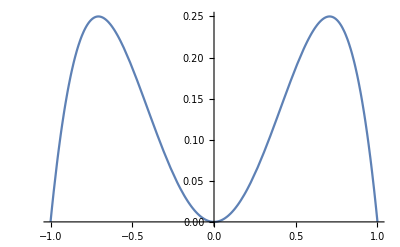

```mathematica
Plot[x^2-x^4,{x,-1,1}]
```